```mathematica
Ns = 4.53389;
u1 = -0.638904880*10^4;
u2 = 0.112005361*10^7;
rsr = 3.126;
rlr = 11.000;
b =-0.13;
rm = 4.209912706;
acf = {-3993.592873, 0, 0.282069372972346137*10^5,0.560425000209256905*10^4, -0.423962138510562945*10^5,-0.598558066508841584*10^5,-0.162613532034769596*10^5,
-0.405142102246254944*10^5, 0.195237415352729586*10^6,0.413823663033582852*10^6,−0.425543284828921501*10^7,0.546674790157210198*10^6,0.663194778861331940*10^8,−0.558341849704095051*10^8,-0.573987344918535471*10^9,0.102010964189156187*10^10,0.300040150506311035*10^10,-0.893187252759830856*10^10,-0.736002541483347511*10^10, 0.423130460980355225*10^11,-0.786351477693491840*10^10,-0.102470557344862152*10^12,0.895155811349267578*10^11, 0.830355322355692902*10^11,-0.150102297761234375*10^12, 0.586778574293387070*10^11 };
C6 = 0.2270032*10^8;
C8 = 0.7782886 *10^9;
C10 = 0.2868869*10^11;
C26 = 0.2819810*10^26;
Aex = 0.1317786*10^5;
gamma = 5.317689;
beta = 2.093816;
ξ[r_]:= (r-rm)/(r+b rm);
uIR[r_]:= Sum[acf[[i+1]]*(ξ[r])^i,{i,0,Length[acf]-1}];
uSR[r_]:= u1 +u2/r^Ns;
uLR[r_]:= -C6/r^6-C8/r^8-C10/r^10-C26/r^26-Aex r^gamma Exp[-beta r];
Singlet[r_]:=Piecewise[{{uSR[r],0<r≤rsr},{uIR[r],rsr<r<rlr},{uLR[r],rlr≤ r}}];
Ns3 = 4.5338950;
u13=-0.619088543*10^3;
u23 = 0.956231677*10^6;
r3sr = 5.07;
b3 =-0.33;
rm3 = 6.0933451;
a3cf = {−241.503352,−0.672503402304666542,0.195494577140503543*10^4,−0.141544168453406223*10^4,−0.221166468149940465*10^4,0.165443726445793004*10^4,−0.596412188910614259*10^4,
0.654481694231538040*10^4,0.261413416681972012*10^5,−0.349701859112702878*10^5,−0.328185277155018630*10^5, 0.790208849885562522*10^5,−0.398783520249289213*10^5};
ξ3[r_]:= (r-rm3)/(r+b3 rm3);
uIR3[r_]:= Sum[a3cf[[i+1]]*(ξ3[r])^i,{i,0,Length[a3cf]-1}];
uSR3[r_]:= u13 +u23/r^Ns3;
uLR3[r_]:= -C6/r^6-C8/r^8-C10/r^10-C26/r^26+Aex r^gamma Exp[-beta r];
Triplet[r_]:=Piecewise[{{uSR3[r],0<r≤r3sr},{uIR3[r],r3sr≤ r≤ rlr},{uLR3[r],rlr≤ r}}];
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/0.529177210903;
Rmax=800;
Rmin=0.005;
NR =10000;
RGrid=Table[Rmin+((i-1)/(NR-1))^3(Rmax-Rmin),{i,1,NR}];
SingletNewdat = Table[{RGrid[[i]]*AngstrominBohr,Singlet[RGrid[[i]]]*invcminHartree},{i,1,NR}];
TripletNewdat = Table[{RGrid[[i]]*AngstrominBohr,Triplet[RGrid[[i]]]*invcminHartree},{i,1,NR}];
SingletNew = Interpolation[SingletNewdat(*,InterpolationOrder->1*)];
TripletNew=Interpolation[TripletNewdat(*,InterpolationOrder->1*)];
```

```mathematica
Rb85AMHz = 1011.9108132;
Rb85gi = -0.00029364006;
Rb85gs = 2.002319313470;
Rb85s = 1/2;
Rb85i = 5/2;
μb = (9.27*10^-24)/(6.626*10^-34)*10^-10;
Rb85ATHz = Rb85AMHz*10^-6;
Rb85Ainvcm = (Rb85ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
Rb85AH = Rb85Ainvcm*invcminHartree;
μbTHz = μb *10^-6;
μbinvcm = (μbTHz *6.626*10^-34*10^12)/(1.986*10^-23);
μbH=μbinvcm*invcminHartree;
```

```mathematica
Rb85HF2atombasis = Flatten[Table[Table[{f1, mf1,f2,mf2},{mf1,-f1,f1},{mf2,-f2,f2}],{f1,2,3},{f2,2,3}],3];
```

```mathematica
Select[Rb85HF2atombasis,#[[2]]+#[[4]]==4&]
```

{{2,2,2,2},{2,1,3,3},{2,2,3,2},{3,2,2,2},{3,3,2,1},{3,1,3,3},{3,2,3,2},{3,3,3,1}}

```mathematica
Rb85MF0basis = {{2,-2,2,2},{2,-2,3,2},{2,-1,2,1},{2,-1,3,1},{2,0,2,0},{2,0,3,0},{2,1,3,-1},{2,2,3,-2},{3,-3,3,3},{3,-2,3,2},{3,-1,3,1},{3,0,3,0}};
```

```mathematica
Rb85MF4basis = {{2,2,2,2},{2,1,3,3},{2,2,3,2},{3,1,3,3},{3,2,3,2}};
```

```mathematica
SingletProjectionSym[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,3]]] KroneckerDelta[Rb85MF4basis[[j,2]],Rb85MF4basis[[j,4]]])(1+KroneckerDelta[Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,3]]] KroneckerDelta[Rb85MF4basis[[jp,2]],Rb85MF4basis[[jp,4]]]))))*(ProjectionMatrixElement[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85s,Rb85i,Rb85s,Rb85i,0]+ProjectionMatrixElement[Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85s,Rb85i,Rb85s,Rb85i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85s,Rb85i,Rb85s,Rb85i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85s,Rb85i,Rb85s,Rb85i,0]),{j,1,Length[Rb85MF4basis]},{jp,1,Length[Rb85MF4basis]}]
```

```mathematica
Rb85SingletProjection={{5/36,-(√(5/3))/6,(√(5/2))/9,(√(5/6))/6,-5/36},{-(√(5/3))/6,1/3,-(√(2/3))/3,-1/(3 √2),(√(5/3))/6},{(√(5/2))/9,-(√(2/3))/3,2/9,1/(3 √3),-(√(5/2))/9},{(√(5/6))/6,-1/(3 √2),1/(3 √3),1/6,-(√(5/6))/6},{-5/36,(√(5/3))/6,-(√(5/2))/9,-(√(5/6))/6,5/36}};
```

```mathematica
N[MatrixForm[Rb85SingletProjection]]
```

(0.138889 | -0.215166 | 0.175682 | 0.152145 | -0.138889
-0.215166 | 0.333333 | -0.272166 | -0.235702 | 0.215166
0.175682 | -0.272166 | 0.222222 | 0.19245 | -0.175682
0.152145 | -0.235702 | 0.19245 | 0.166667 | -0.152145
-0.138889 | 0.215166 | -0.175682 | -0.152145 | 0.138889)

```mathematica
TripletProjectSym[p_,l_]:=Table[(1/(2√((1+KroneckerDelta[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,3]]] KroneckerDelta[Rb85MF4basis[[j,2]],Rb85MF4basis[[j,4]]])(1+KroneckerDelta[Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,3]]] KroneckerDelta[Rb85MF4basis[[jp,2]],Rb85MF4basis[[jp,4]]]))))*(ProjectionMatrixElement[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85s,Rb85i,Rb85s,Rb85i,1]+ProjectionMatrixElement[Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85s,Rb85i,Rb85s,Rb85i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85s,Rb85i,Rb85s,Rb85i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85s,Rb85i,Rb85s,Rb85i,1]),{j,1,Length[Rb85MF4basis]},{jp,1,Length[Rb85MF4basis]}]
```

```mathematica
Rb85TripletProjection=FullSimplify[TripletProjectSym[0,0]]
```

```mathematica
Rb85TripletProjection= IdentityMatrix[5]-Rb85SingletProjection
```

```mathematica
Rb85TripletProjection={{31/36,(√(5/3))/6,-(√(5/2))/9,-(√(5/6))/6,5/36},{(√(5/3))/6,2/3,(√(2/3))/3,1/(3 √2),-(√(5/3))/6},{-(√(5/2))/9,(√(2/3))/3,7/9,-1/(3 √3),(√(5/2))/9},{-(√(5/6))/6,1/(3 √2),-1/(3 √3),5/6,(√(5/6))/6},{5/36,-(√(5/3))/6,(√(5/2))/9,(√(5/6))/6,31/36}};
```

```mathematica
N[MatrixForm[Rb85TripletProjection]]
```

(0.861111 | 0.215166 | -0.175682 | -0.152145 | 0.138889
0.215166 | 0.666667 | 0.272166 | 0.235702 | -0.215166
-0.175682 | 0.272166 | 0.777778 | -0.19245 | 0.175682
-0.152145 | 0.235702 | -0.19245 | 0.833333 | 0.152145
0.138889 | -0.215166 | 0.175682 | 0.152145 | 0.861111)

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_,μb_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μb B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μb B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

```mathematica
HZsym[p_,l_,B_]:=
Table[(1/(√((1+KroneckerDelta[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,3]]] KroneckerDelta[Rb85MF4basis[[j,2]],Rb85MF4basis[[j,4]]])(1+KroneckerDelta[Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,3]]] KroneckerDelta[Rb85MF4basis[[jp,2]],Rb85MF4basis[[jp,4]]]))))*(HZ[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85s,Rb85i,Rb85gs,Rb85gi,Rb85AH,B,μbH]KroneckerDelta[Rb85MF4basis[[j,3]],Rb85MF4basis[[jp,3]]]KroneckerDelta[Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,4]]]+HZ[Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85s,Rb85i,Rb85gs,Rb85gi,Rb85AH,B,μbH]KroneckerDelta[Rb85MF4basis[[j,1]],Rb85MF4basis[[jp,1]]]KroneckerDelta[Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,2]]]+(-1)^p(-1)^l HZ[Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85s,Rb85i,Rb85gs,Rb85gi,Rb85AH,B,μbH]KroneckerDelta[Rb85MF4basis[[j,1]],Rb85MF4basis[[jp,3]]]KroneckerDelta[Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,4]]]+(-1)^p(-1)^l HZ[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85s,Rb85i,Rb85gs,Rb85gi,Rb85AH,B,μbH]KroneckerDelta[Rb85MF4basis[[j,3]],Rb85MF4basis[[jp,1]]]KroneckerDelta[Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,2]]]),{j,1,Length[Rb85MF4basis]},{jp,1,Length[Rb85MF4basis]}];
```

```mathematica
HZRb85[B_]=FullSimplify[HZsym[0,0,B]];
```

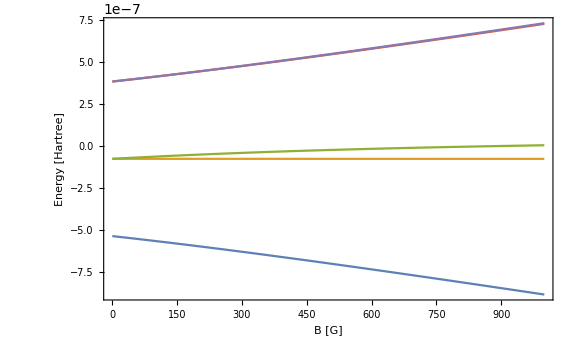

```mathematica
EigenSystemRb85[B_]:= Sort[Transpose[Eigensystem[HZRb85[B]]]];
Plot[{EigenSystemRb85[B][[1]][[1]],EigenSystemRb85[B][[2]][[1]],EigenSystemRb85[B][[3]][[1]],EigenSystemRb85[B][[4]][[1]],EigenSystemRb85[B][[5]][[1]]},{B,0,1000},ImageSize->Large,Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},LabelStyle->Large]
```

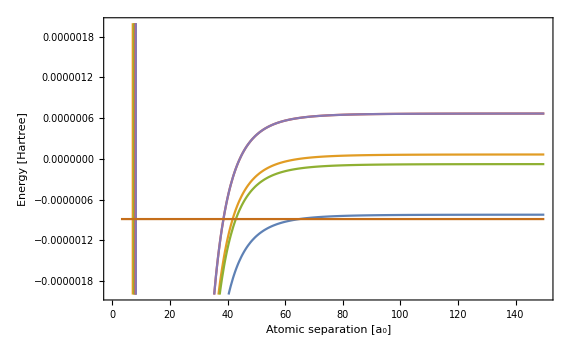

```mathematica
Htotal[r_,B_]= HZRb85[B]+Rb85TripletProjection*TripletNew[r]+Rb85SingletProjection*SingletNew[r];
Plot[{ Htotal[r, 1000][[1, 1]], Htotal[r, 1000][[2, 2]],Htotal[r, 1000][[3, 3]],Htotal[r, 1000][[4, 4]],Htotal[r, 1000][[5, 5]], EigenSystemRb85[1000][[1]][[1]]},{r,3,150},Frame->True,ImageSize->Large,FrameLabel->{"Atomic separation [a_0]","Energy [Hartree]"},LabelStyle->Large,PlotRange->{-2*10^-6,2*10^-6}]
```

```mathematica
βRb85 = 
β/.Solve[(-C6*AngstrominBohr^6*invcminHartree)/β^6-(C8*AngstrominBohr^8*invcminHartree)/β^8-(C10*AngstrominBohr^10*invcminHartree)/β^10==-1/(2 μRb85 β^2),β][[8]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

164.507

```mathematica
BohrinRb85vdw = 1/164.50715895764995;
Rb85vdwinHartree = 1/(2 μRb85 βRb85^2);
HartreeinRb85vdw = 1/Rb85vdwinHartree;
```

```mathematica
C6vdw = (2 μRb85)/βRb85^4(C6*invcminHartree*AngstrominBohr^6);
C8vdw = (2 μRb85)/βRb85^6(C8*invcminHartree*AngstrominBohr^8);
C10vdw = (2 μRb85)/βRb85^8(C10*invcminHartree*AngstrominBohr^10);
C26vdw = (2 μRb85)/βRb85^24(C26*invcminHartree*AngstrominBohr^26);
```

```mathematica
μbvdw = μbH*HartreeinRb85vdw;
TripletVDWdat= Table[{TripletNewdat[[i,1]]*BohrinRb85vdw, TripletNewdat[[i,2]]*HartreeinRb85vdw},{i,1,Length[TripletNewdat]}];
TripletVDW= Interpolation[TripletVDWdat];
SingletVDWdat= Table[{SingletNewdat[[i,1]]*BohrinRb85vdw, SingletNewdat[[i,2]]*HartreeinRb85vdw},{i,1,Length[SingletNewdat]}];
SingletVDW= Interpolation[SingletVDWdat];
Rb85vlr[r_]:= -C6vdw/r^6-C8vdw/r^8-C10vdw/r^10(*-C26vdw/r^26*);
```

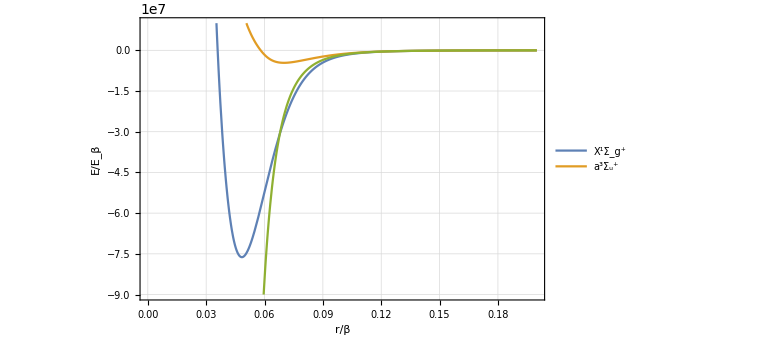

```mathematica
Plot[{SingletVDW[r],TripletVDW[r],Rb85vlr[r]},{r,0.02,0.2},PlotRange->{-9.0*10^7,10^7},ImageSize->Large,GridLines->Automatic,Frame->True,FrameLabel->{"r/β","E/E_β"},LabelStyle->Medium,PlotLegends->{"X^1Σ_g^+","a^3Σ_u^+"}]
```

```mathematica
rx = 0.075;
rf = 5.0;
r0 = 0.25;
rmin = 0.03;
rmax = r0;
ltest = 0;
Etest = 10^-16; 
ksqr[Ε_,l_,r_]:=(Ε - Rb85vlr[r]-(l(l+1))/r^2);
BC1[Ε_,l_,r_,rx_]:=1/Sqrt[(Ε - Rb85vlr[r]-(l(l+1))/r^2)^(1/2)]/.r->rx;
BC2[Ε_,l_,r_,rx_]:=D[1/Sqrt[(Ε - Rb85vlr[r]-(l(l+1))/r^2)^(1/2)],r]/.r->rx;
α0sol=Flatten[Table[NDSolve[{α''[r]+ksqr[Etest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[Etest,ltest,r,rx],α'[rx]==BC2[Etest,ltest,r,rx]},α,{r,rx,rf}],{ltest,0,2}]];
α0fun=Table[α/.α0sol[[i]],{i,1,Length[α0sol]}];
nr=300;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(α0fun[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,2}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,2}];
phivals=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0fun[[ltest+1]],phaseintfun[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,2}],{rf,rGrid}]];
ϕRb85=Table[phivals[[i,nr,2]],{i,1,Length[phivals]}];
```

```mathematica
Rb85SingletQD=CalcQuantumDefect[10^-16,0,rmin,rmax,r0,rx,r0,r,nr,SingletVDW,ϕRb85[[1]]]
```

-0.489942

```mathematica
Rb85TripletQD=CalcQuantumDefect[10^-16,0,rmin,rmax,r0,rx,r0,r,nr,TripletVDW,ϕRb85[[1]]]
```

0.447506

```mathematica
Rb85Avdw=Rb85AH*HartreeinRb85vdw;
Rb85HZVDW[p_,l_,B_]:=
Table[(1/(√((1+KroneckerDelta[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,3]]] KroneckerDelta[Rb85MF4basis[[j,2]],Rb85MF4basis[[j,4]]])(1+KroneckerDelta[Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,3]]] KroneckerDelta[Rb85MF4basis[[jp,2]],Rb85MF4basis[[jp,4]]]))))*(HZ[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85s,Rb85i,Rb85gs,Rb85gi,Rb85Avdw,B,μbvdw]KroneckerDelta[Rb85MF4basis[[j,3]],Rb85MF4basis[[jp,3]]]KroneckerDelta[Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,4]]]+HZ[Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85s,Rb85i,Rb85gs,Rb85gi,Rb85Avdw,B,μbvdw]KroneckerDelta[Rb85MF4basis[[j,1]],Rb85MF4basis[[jp,1]]]KroneckerDelta[Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,2]]]+(-1)^p(-1)^l HZ[Rb85MF4basis[[j,3]],Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,1]],Rb85MF4basis[[jp,2]],Rb85s,Rb85i,Rb85gs,Rb85gi,Rb85Avdw,B,μbvdw]KroneckerDelta[Rb85MF4basis[[j,1]],Rb85MF4basis[[jp,3]]]KroneckerDelta[Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,4]]]+(-1)^p(-1)^l HZ[Rb85MF4basis[[j,1]],Rb85MF4basis[[j,2]],Rb85MF4basis[[jp,3]],Rb85MF4basis[[jp,4]],Rb85s,Rb85i,Rb85gs,Rb85gi,Rb85Avdw,B,μbvdw]KroneckerDelta[Rb85MF4basis[[j,3]],Rb85MF4basis[[jp,1]]]KroneckerDelta[Rb85MF4basis[[j,4]],Rb85MF4basis[[jp,2]]]),{j,1,Length[Rb85MF4basis]},{jp,1,Length[Rb85MF4basis]}];
```

```mathematica
Rb85HZ[B_]=FullSimplify[Rb85HZVDW[0,0,B]];
```

```mathematica
Rb85HVDW[r_,B_]=Rb85HZ[B]+Rb85TripletProjection*TripletVDW[r]+Rb85SingletProjection*SingletVDW[r];
Rb85Eigensystem[B_]:= Sort[Transpose[Eigensystem[Rb85HZ[B]]]];
```

```mathematica
DD[B_]:= Transpose[{Rb85Eigensystem[B][[1]][[2]],Rb85Eigensystem[B][[2]][[2]],Rb85Eigensystem[B][[3]][[2]],Rb85Eigensystem[B][[4]][[2]],Rb85Eigensystem[B][[5]][[2]]}];
Rb85Eth[B_]:= Table[Rb85Eigensystem[B][[j]][[1]],{j,1,Length[Rb85MF4basis]}];
```

```mathematica
Rb85HVDWRotated[r_,B_]:= Transpose[DD[B]].Rb85HVDW[r,B].DD[B];
```

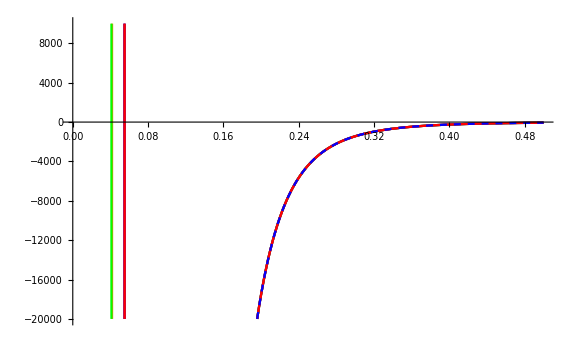

```mathematica
Plot[{Rb85HVDWRotated[r,1000][[1,1]]-Rb85Eth[1000][[1]],Rb85HVDWRotated[r,1000][[2,2]]-Rb85Eth[1000][[2]],Rb85HVDWRotated[r,1000][[3,3]]-Rb85Eth[1000][[3]],Rb85HVDWRotated[r,1000][[4,4]]-Rb85Eth[1000][[4]],Rb85HVDWRotated[r,1000][[5,5]]-Rb85Eth[1000][[5]],(*, Rb85Eth[1000][[1]]+10^-5,*)Rb85vlr[r]},{r,0.03,0.5},PlotRange->{-20000,10000},ImageSize->Large, PlotStyle->{Blue, Orange,Green, Purple, Red, {Blue,Dashed},{Black,Dashed}}]
```

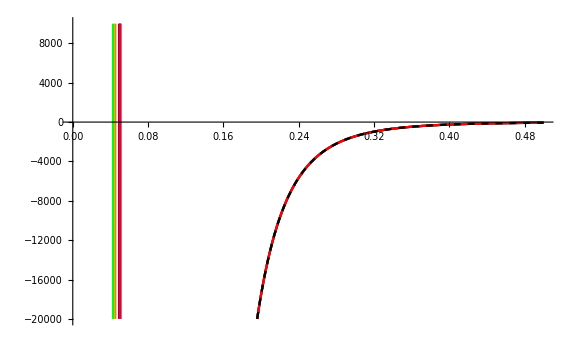

```mathematica
Plot[{Rb85HVDWRotated[r,100][[1,1]]-Rb85Eth[100][[1]],Rb85HVDWRotated[r,100][[2,2]]-Rb85Eth[100][[2]],Rb85HVDWRotated[r,100][[3,3]]-Rb85Eth[100][[3]],Rb85HVDWRotated[r,100][[4,4]]-Rb85Eth[100][[4]],Rb85HVDWRotated[r,100][[5,5]]-Rb85Eth[100][[5]],(*, Rb85Eth[1000][[1]]+10^-5,*)Rb85vlr[r]},{r,0.03,0.5},PlotRange->{-20000,10000},ImageSize->Large, PlotStyle->{Blue, Orange,Green, Purple, Red,{Black,Dashed}}]
```

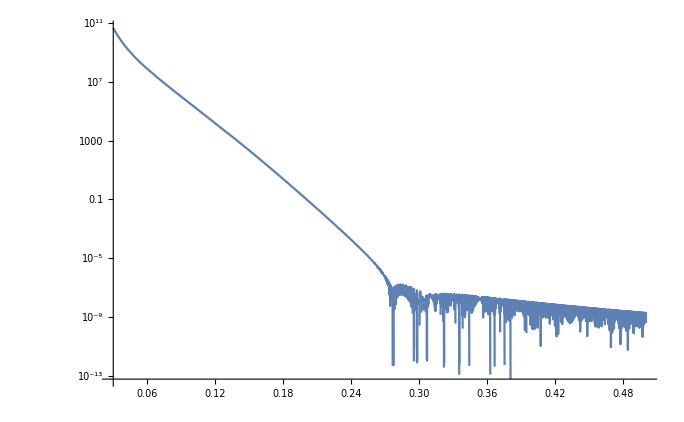

```mathematica
LogPlot[{Abs[Rb85HVDWRotated[r,100][[1,1]]-Rb85Eth[100][[1]]-Rb85vlr[r]]},{r,0.03,0.5}]
```

Energy-Dependent Calculation at a Single Magnetic Field (i.e., B = 0)

```mathematica
Rb85HZerofield[r_] = Rb85HVDW[r,0];
```

```mathematica
Rb85EthZerofield = Rb85Eth[0]
```

{-2255.26,-322.18,-322.18,1610.9,1610.9}

```mathematica
SingletQD = Rb85SingletQD;
TripletQD =Rb85TripletQD;
KsrFTEI=Rb85SingletProjection*Tan[π SingletQD] + Rb85TripletProjection*Tan[π TripletQD];
KsrFTEIPP= KsrFTEI[[1,1]];
KsrFTEIQP=KsrFTEI[[2;;5,1]];
KsrFTEIPQ=KsrFTEI[[1,2;;5]];
KsrFTEIQQ=KsrFTEI[[2;;5,2;;5]];
```

```mathematica
En=300;
Emin = 10^-16;
Emax =5000;
EGrid=Table[Emin+((i-1)/(En-1))^3(Emax-Emin),{i,1,En}];
```

```mathematica
calcTanGamma[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{αfun,phaseint,g0,g0p,f0,f0p,αp,α,κ,rp,gbound,gboundp,tanγ},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
κ=√-Ε;
gbound=√(κ/π rp) BesselK[l+1/2,κ rp]/.rp->rf;
gboundp=D[√(κ/π rp) BesselK[l+1/2,κ rp],rp]/.rp->rf;
tanγ =-(gbound g0p-gboundp g0)/(gbound f0p - gboundp f0);
Return[tanγ]
]
gammaTable=Table[{-EGrid[[ii]],ArcTan[calcTanGamma[0,rx,rf,r,-EGrid[[ii]],ϕRb85[[1]]]]},{ii,1,Length[EGrid]}];
```

```mathematica
GammaTablenew=gammaTable;
For[i=1,i<Length[gammaTable],i++,
If[(gammaTable[[i+1,2]]-gammaTable[[i,2]]<-1.2),Print[i];
GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]+π,GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]]]
```

52

139

225

```mathematica
Gammafun = Interpolation[GammaTablenew(*,InterpolationOrder->1*)];
```

```mathematica
CotGamma2[Ε_]:= Cot[Gammafun[((Rb85EthZerofield[[1]]+Ε)-Rb85EthZerofield[[2]])]];
CotGamma3[Ε_]:= Cot[Gammafun[((Rb85EthZerofield[[1]]+Ε)-Rb85EthZerofield[[3]])]];
CotGamma4[Ε_]:= Cot[Gammafun[((Rb85EthZerofield[[1]]+Ε)-Rb85EthZerofield[[4]])]];
CotGamma5[Ε_]:= Cot[Gammafun[((Rb85EthZerofield[[1]]+Ε)-Rb85EthZerofield[[5]])]];
CotGammaMatrix[Ε_]:=DiagonalMatrix[{CotGamma2[Ε],CotGamma3[Ε],CotGamma4[Ε],CotGamma5[Ε]}];
```

```mathematica
Emin = 10^-15*HartreeinRb85vdw
Emax = 1.6*10^-7*HartreeinRb85vdw
```

4.18888×10^-6

670.221

```mathematica
KtildeFTEI[Ε_]:= KsrFTEIPP-KsrFTEIPQ.Inverse[KsrFTEIQQ+CotGammaMatrix[Ε]].KsrFTEIQP;
```

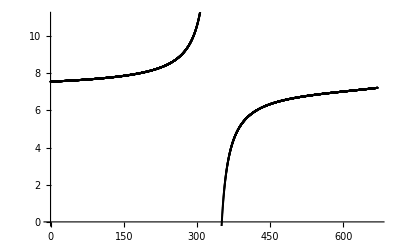

```mathematica
ListPlot[{Table[{Etest,KtildeFTEI[Etest]},{Etest,Emin,Emax,10^-1}]},PlotStyle->{Black,Red}]
```

```mathematica
CalcTanEta[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,gs,fs,fsp,gsp,k,tanη,αfun,phaseint,α,αp},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs =g[l,k,r];
gsp=dgdr[l,k,r];
tanη=(fs f0p-f0 fsp)/(gs f0p-f0 gsp)/.r->rf;
Return[tanη]
]
EtaTable=Table[{EGrid[[ii]],ArcTan[CalcTanEta[ltest,rx,rf,r,EGrid[[ii]],ϕRb85[[1]]]]},{ii,1,Length[EGrid]}];
```

```mathematica
EtaTablenew2=EtaTable;
For[i=1,i<Length[EtaTable],i++,
If[(EtaTable[[i+1,2]]-EtaTable[[i,2]]>1.2),Print[i];
EtaTablenew2[[i+1;;Length[EtaTable],2]]=EtaTablenew2[[i+1;;Length[EtaTable],2]]-π,EtaTablenew2[[i+1;;Length[EtaTable],2]]=EtaTablenew2[[i+1;;Length[EtaTable],2]]]
]
```

36

79

121

164

206

247

289

```mathematica
Etafun=Interpolation[EtaTablenew2,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
CalcA[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,fs,fsp,gs,gsp,k,A,αfun,phaseint,α,αp,tanη,Wfsf0,Wgsf0,Wfsg0,Wgsg0},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
f0=αfun[rf]Sin[ϕ+phaseint];
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,rf];
fsp=dfdr[l,k,rf];
gs=g[l,k,rf];
gsp=dgdr[l,k,rf];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
A=-((Wfsg0 -tanη Wgsg0)/(Wgsf0+tanη Wfsf0));
Return[A]
]
ATable=Table[{EGrid[[ii]],CalcA[ltest,rx,rf,r,EGrid[[ii]],ϕRb85[[1]]]},{ii,1,Length[EGrid]}];
```

```mathematica
Afun = Interpolation[ATable,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
CalcG[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,k,tanη,G,fs,fsp,gs,gsp,αfun,phaseint,Wfsf0,Wgsf0,Wfsg0,Wgsg0,α,αp},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
f0=αfun[rf]Sin[ϕ+phaseint];
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[ Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs=g[l,k,r];
gsp=dgdr[l,k,r];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
G=-(Wfsg0*Wfsf0+Wgsg0*Wgsf0)/(Wfsf0^2+Wgsf0^2)/.r->rf;
Return[G]
]
GTable=Table[{EGrid[[ii]],CalcG[ltest,rx,rf,r,EGrid[[ii]],ϕRb85[[1]]]},{ii,1,Length[EGrid]}];
```

```mathematica
Gfun =Interpolation[GTable,InterpolationOrder->1];
```

```mathematica
KFTEIfun[Etest_]:= Sqrt[Afun[Etest]](KtildeFTEI[Etest]^-1+Gfun[Etest])^-1 Sqrt[Afun[Etest]];
```

```mathematica
cotdeltafun[Ε_]:=(1-Tan[Etafun[Ε]]KFTEIfun[Ε])/(Tan[Etafun[Ε]]+KFTEIfun[Ε]);
```

```mathematica
SigmaTable =Table[{iE,(4 π)/(iE)(Sin[ArcCot[cotdeltafun[iE]]])^2},{iE,Emin,Emax,10^-1}];
```

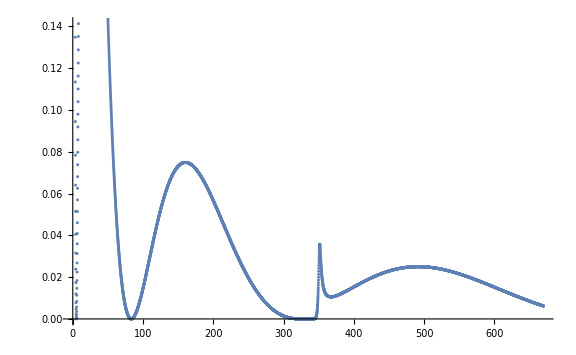

```mathematica
ListPlot[SigmaTable,ImageSize->Large]
```

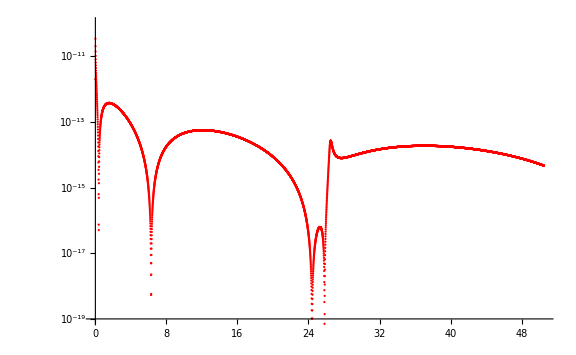

```mathematica
PMQDT =ListLogPlot[Table[{SigmaTable[[i]][[1]]*Rb85vdwinHartree*1/(3.1668115634556*10^-15)*10^-6,SigmaTable[[i]][[2]]*(1/BohrinRb85vdw)^2*(5.2917724900001*10^-9)^2},{i,1,Length[SigmaTable]}],ImageSize->Large,PlotStyle->Red,PlotRange->{10^-19,10^-10}]
```

```mathematica
Rb85logderdat = Import["/Users/alysonlaskowski/Alkali-Scattering/Rb85FR.dat"];
```

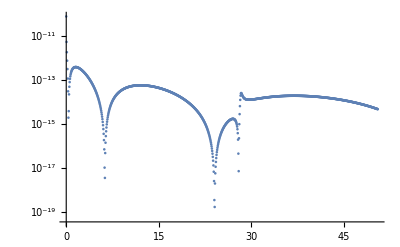

```mathematica
PLOGDER = ListLogPlot[Rb85logderdat]
```

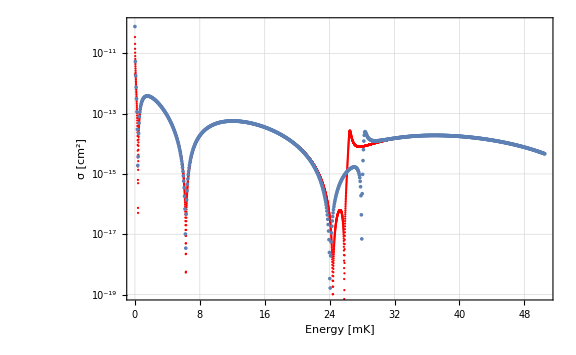

```mathematica
Show[PMQDT,PLOGDER,Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->Large,FrameLabel->{"Energy [mK]", "σ [cm^2]"}]
```